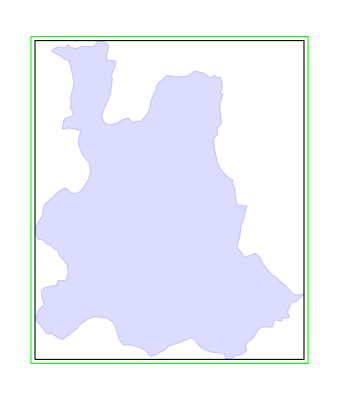

```mathematica
(*==========================*
|Load Input Data& Bounds|
*==========================*)(*Load the region boundary from a GeoTIFF file*)RegBound=QuantityMagnitude[Import["~/Dropbox/Mapping/WSF2019/WestBurkina/HouetRegion.tif",{"GeoTIFF","SpatialRange"}]][[{2,1}]];

(*Load the 100m resolution raster data and normalize*)
hou100m=Transpose[Import["~/Dropbox/Mapping/WSF2019/WestBurkina/HouetRegion100.tif","Data"]]*(1./255);

(*============================*
|Create Houet Border Polygon|
*============================*)

h=Import["~/Dropbox/Mapping/WSF2019/WestBurkina/houet.geojson"];
polygons=Cases[h,_Polygon,Infinity];
vertices=polygons/. Polygon[pts_]:>pts;
HouLatLon=Flatten[vertices,1][[2]];
HouLatLon[[All,2]]-=0.07; (*Adjust longitude*)

Hou=RegionMember[Polygon[HouLatLon]];
dim=Dimensions[hou100m];

br=BoundingRegion[Polygon[HouLatLon]];
buf=2;
bds={br[[1]]+{-buf,-buf}/110,br[[2]]+{buf,buf}/110};
reg[pt_,bds_]:=If[pt[[1]]>bds[[1,1]]&&pt[[1]]<bds[[2,1]]&&pt[[2]]>bds[[1,2]]&&pt[[2]]<bds[[2,2]],True,False];
Show[Graphics[{{EdgeForm[Blue],FaceForm[Lighter[Blue,0.1]],Opacity[0.15],Polygon[HouLatLon]},{EdgeForm[Black],FaceForm[None],br},{EdgeForm[Green],FaceForm[None],Rectangle[bds[[1]],bds[[2]]]}}]]
```

```mathematica
(*==========================*
|Define Coordinates for Raster|
*==========================*)

(*X-coordinates*)
xcoord=Table[RegBound[[1,1]]+(x-1)/(dim[[1]]-1)*(RegBound[[1,2]]-RegBound[[1,1]]),{x,dim[[1]]}];

(*Y-coordinates*)
ycoord=Table[RegBound[[2,2]]-(y-1)/(dim[[2]]-1)*(RegBound[[2,2]]-RegBound[[2,1]]),{y,dim[[2]]}];

(*==========================*
|Create 1km Resolution Raster|
*==========================*)

hou1k=Table[N[Mean[Mean[hou100m[[1+10 (i-1);;10 i,1+10 (j-1);;10 j]]]]],{i,dim[[1]]/10},{j,dim[[2]]/10}];

(*Generate corresponding coordinates for 1km raster*)
hou1kCoo=Table[{N[Mean[xcoord[[1+10 (i-1);;10 i]]]],N[Mean[ycoord[[1+10 (j-1);;10 j]]]]},{i,dim[[1]]/10},{j,dim[[2]]/10}];

(*==========================*
|Define Thresholds& Select Occupied Squares|
*==========================*)

thresholds={0.05,2/110.,5/110,0.05,1/110.}; 
(*thresholds: 
1: building density in 1km squares to classify as occupied; 2: isolation distance (km from other occupied cells) to be considered as potential study village;
3: minimum distance from other study villages to be included;
4: building density in 100m squares to classify as occupied; *)

(*Select occupied 1km squares based on threshold*)
hou1kSelect=(UnitStep[hou1k-thresholds[[1]]]*hou1k)/. {0.->0};
(*Count number of occupied squares*)
Print[{"Number of occupied in region",Dimensions[hou1k][[1]]Dimensions[hou1k][[2]]-Count[Flatten[hou1kSelect],0]}];

(*------------Generate coordinate list of occupied cells-----------------------*)
(*------------------------------------------------------------------------------------------------Coo1km colums: 1=x-coor, 2=ycoord, 3=building density, 4=type(0 - ouside hou, 1=inside Hou, 2=Potential release site)
--------------------------------------------------------------------*)
Coo1km={};
Do[If[hou1kSelect[[i,j]]>0 &&reg[hou1kCoo[[i,j]],bds],AppendTo[Coo1km,Flatten[{hou1kCoo[[i,j]],hou1kSelect[[i,j]],0}]]],{i,Length[hou1kSelect]},{j,Length[hou1kSelect[[1]]]}];
Print[{"Number of occupied in subregion",Length[Coo1km]}];

(*Mark cells inside Houet region - assign these to type=1*)
Do[If[Hou[Coo1km[[i,{1,2}]]],Coo1km[[i,4]]=1],{i,Length[Coo1km]}];
(*==========================*
|Select Isolated Sites|
*==========================*)
Isol={};
Do[dis=Min[Table[EuclideanDistance[Coo1km[[i,{1,2}]],Coo1km[[j,{1,2}]]],{j,Delete[Range[Length[Coo1km]],i]}]];
If[dis>thresholds[[2]]&&Coo1km[[i,4]]==1,AppendTo[Isol,i]],{i,Length[Coo1km]}];
Print[{"number of isolated villages in Hou",Length[Isol]}];

(*==========================*
|Determine Potential Release Sites  - assign these to type=2 & put in column 4 of Coo1km |
*==========================*)

order=RandomSample[Isol,Length[Isol]];
RelSites={Coo1km[[order[[1]],{1,2}]]};
Coo1km[[order[[1]],4]]=2;

Do[site=order[[i]];
dis=Min[Table[EuclideanDistance[Coo1km[[site,{1,2}]],RelSites[[j]]],{j,Length[RelSites]}]];
If[dis>thresholds[[3]],AppendTo[RelSites,Coo1km[[order[[i]],{1,2}]]];
Coo1km[[order[[i]],4]]=2],{i,2,Length[order],1}];

Print[{"number of potential release sites",Length[RelSites]}];
(*-----------------------------------------------------------------------------------*)
```

{Number of occupied in region,1183}

{Number of occupied in subregion,857}

{number of isolated villages in Hou,86}

{number of potential release sites,69}

```mathematica
(*==========================*
|Assign Random Sample Data|
*==========================*)

(*num=Import["~/Dropbox/FieldTrials/CRT/CoordSets/No. mosq per human kpt7.csv","Table"]//Flatten;*)

num=Import["~/Dropbox/FieldTrials/CRT/CoordSets/max_no_mosq_2018_4000.csv","Table"]//Flatten;
Do[Coo1km[[i]]=Join[Coo1km[[i]],RandomSample[num,1]],{i,Length[Coo1km]}];

(*Export Data*)
(*Export["~/Dropbox/FieldTrials/CRT/GeneralMetapop/InputData/Coo1K002.txt",Coo1km,"Table"];*)
```

```mathematica
(*==========================*
|Process 100m Resolution Data|
*==========================*)
hou100mSelect=(UnitStep[hou100m-thresholds[[4]]]*hou100m)/. {0.->0};

Coo100={};
Do[If[hou100mSelect[[i,j]]>0&&reg[{xcoord[[i]],ycoord[[j]]},bds],AppendTo[Coo100,{xcoord[[i]],ycoord[[j]],hou100m[[i,j]],0,0,0,0}]],{i,Length[hou100mSelect]},{j,Length[hou100mSelect[[1]]]}];

Print[{"num occ hectares = ",Length[Coo100]}];
```

{num occ hectares = ,75736}

```mathematica
(*thresholds[[4]]=0.1;thresholds[[1]]=0.1;
hou100mSelect=(UnitStep[hou100m-thresholds[[4]]])/. {0.->0};
hou1kSelect=(UnitStep[hou1k-thresholds[[1]]])/. {0.->0};
Total[Flatten[hou1kSelect]]
Total[Flatten[hou100mSelect]]*)
```

658

72262

```mathematica
(*==========================*
|Assign 1km Nearest Site|
*==========================*)
(*---position of release sites in 1km set*)
posRel=Position[Coo1km[[All,4]],2]//Flatten;
(*---------------------------------------*)
(*----Assign random factors to 100m set based on random factor of nearest 1km cell----*)
Do[pp=Nearest[Coo1km[[All,{1,2}]],Coo100[[i,{1,2}]]][[1]];
pos=Position[Coo1km[[All,{1,2}]],pp][[1,1]];
Coo100[[i,{4,5,6}]]={Coo1km[[pos,5]],0,pos},{i,Length[Coo100]}];
(*---------------------------------------*)
(*---- assign types to 100m set. 0= outside Hou; 1=Inside Hou; 2 = within 1km of release; 3 = release cell*)
Do[If[Hou[Coo100[[j,{1,2}]]],Coo100[[j,5]]=1],{j,Length[Coo100]}];
Do[
pt=Coo1km[[posRel[[i]],{1,2}]];
Do[If[EuclideanDistance[Coo100[[j,{1,2}]],pt]<thresholds[[5]],Coo100[[j,5]]=2;Coo100[[j,7]]=i],{j,Length[Coo100]}];
(*Print[{i,pt}];*)
near=Nearest[Coo100[[All,{1,2}]],pt][[1]];
index=Position[Coo100[[All,{1,2}]],near][[1,1]];
Coo100[[index,5]]=3,{i,Length[posRel]}];
```

```mathematica
(*Export["~/Dropbox/FieldTrials/CRT/GeneralMetapop/InputData/Coo100m002.txt",Coo100,"Table"];*)
Export["~/Dropbox/FieldTrials/CRT/CRTModel/InputData/Coo100m005.txt",Coo100,"Table"];
Export["~/Dropbox/FieldTrials/CRT/CRTModel/InputData/Coo1K005.txt",Coo1km,"Table"];
```

```mathematica
(*pos=Position[Coo100[[All,5]],2]//Flatten;
PotRel=Coo100[[pos]];
PotRel1km=Union[PotRel[[All,6]]];
Do[
pos=Position[Coo100[[All,6]],PotRel1km[[i]]]//Flatten;
Print[{i,Length[pos]}];
mean=Mean[Coo100[[pos,{1,2}]]];
near=Nearest[Coo100[[pos,{1,2}]],mean][[1]];
index=Position[Coo100[[All,{1,2}]],near][[1,1]];
Coo100[[index,5]]=3,{i,Length[PotRel1km]}];

(*Export 100m coordinate data*)
Export["~/Dropbox/FieldTrials/CRT/GeneralMetapop/InputData/Coo100m002.txt",Coo100,"Table"];*)
```

```mathematica
bds
```

{{-4.83937,10.7224},{-3.63157,12.1505}}

{29199,43119,3348,70}

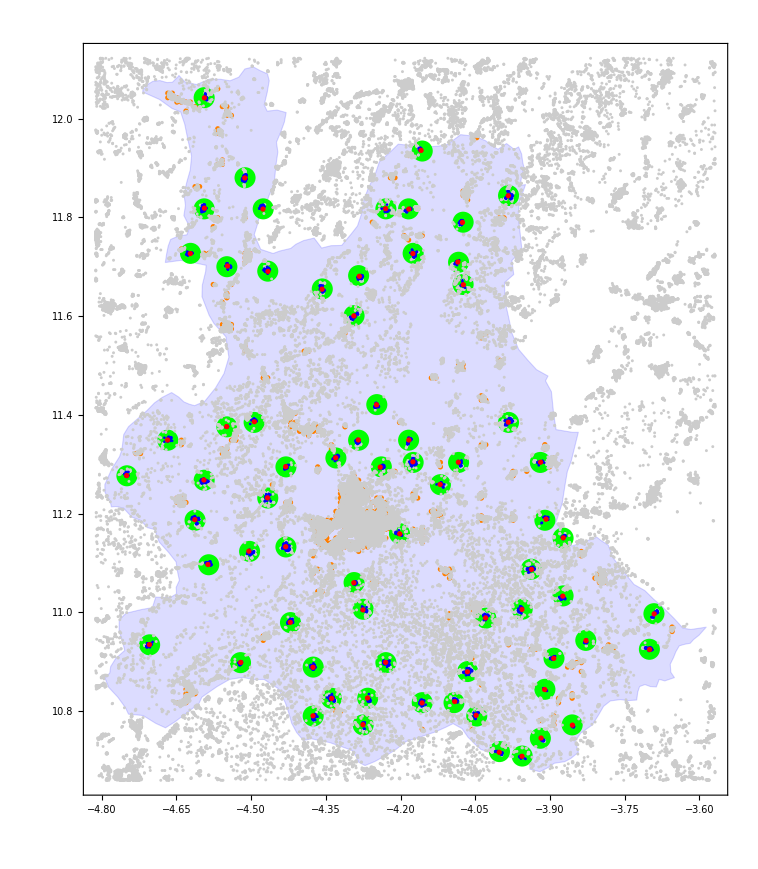

```mathematica
posall=Table[Flatten[Position[Coo100[[All,5]],i]],{i,0,3,1}];
Print[Map[Length,posall]];
posall1km=Table[Flatten[Position[Coo1km[[All,4]],i]],{i,0,2,1}];
Show[Graphics[{EdgeForm[Blue],FaceForm[Lighter[Blue,0.1]],Opacity[0.15],Polygon[HouLatLon]}],ListPlot[Table[Coo1km[[posall1km[[i]],{1,2}]],{i,2,Length[posall1km],1}],PlotStyle->{{Orange,PointSize[0.005]},{Green,PointSize[0.02]}}],ListPlot[Table[Coo100[[posall[[i]],{1,2}]],{i,1,Length[posall],1}],PlotStyle->{GrayLevel[0.8],GrayLevel[0.8],{Blue,PointSize[0.0025]},{Red,PointSize[0.005]}}],Frame->True,AspectRatio->dim[[2]]/dim[[1]],PlotRange->{{bds[[1,1]],bds[[2,1]]},{bds[[1,2]],bds[[2,2]]}}]
```

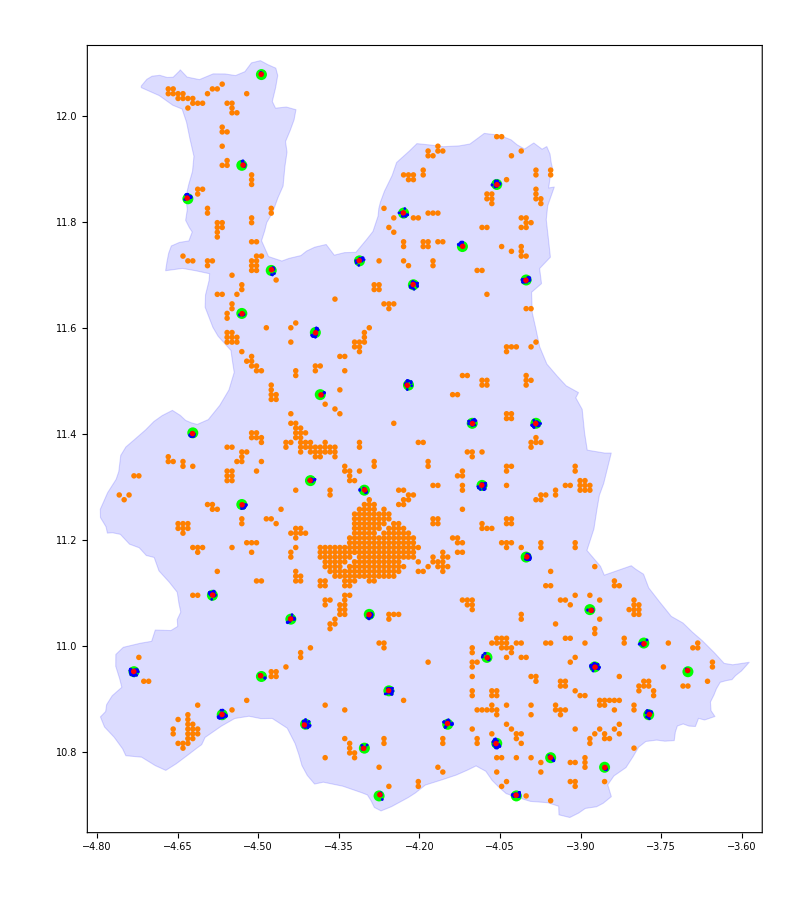

```mathematica
posall=Table[Flatten[Position[Coo100[[All,5]],i]],{i,0,3,1}];
posall1km=Table[Flatten[Position[Coo1km[[All,4]],i]],{i,0,2,1}];
Show[Graphics[{EdgeForm[Blue],FaceForm[Lighter[Blue,0.1]],Opacity[0.15],Polygon[HouLatLon]}],ListPlot[Table[Coo1km[[posall1km[[i]],{1,2}]],{i,2,Length[posall1km],1}],PlotStyle->{{Orange,PointSize[0.005]},{Green,PointSize[0.01]}}],ListPlot[Table[Coo100[[posall[[i]],{1,2}]],{i,3,Length[posall],1}],PlotStyle->{(*GrayLevel[0.8],GrayLevel[0.8],*){Blue,PointSize[0.0025]},{Red,PointSize[0.005]}}],Frame->True,AspectRatio->dim[[2]]/dim[[1]],PlotRange->{{First[xcoord],Last[xcoord]},{First[ycoord],Last[ycoord]}}]
```

```mathematica
dim
```

{1645,1887}

```mathematica
Coo1km[[1;;5]]
```

{{-4.99589,11.6281,0.0470799,0,9.91388},{-4.99589,11.6191,0.011669,0,19.9712},{-4.99589,11.0422,0.0488912,0,11.3476},{-4.99589,11.0332,0.0106336,0,12.416},{-4.99589,10.9791,0.0226659,0,30.4598}}